```mathematica
t1a=4;t1r=.4; cc=horse8;
{numPT,pt,ct,kft,oit,olt,isE}=getNumParent[cc];isoTable=startIsoTable[pt,cc];
kthIter=1;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest2[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum
```

256

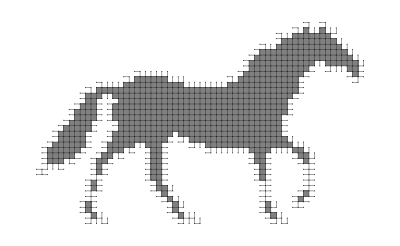

```mathematica
showCC2D[restoreAfterEThinning2[kft,cc]]
```

415

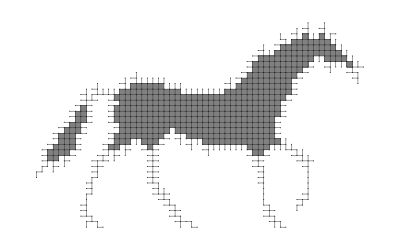

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

319

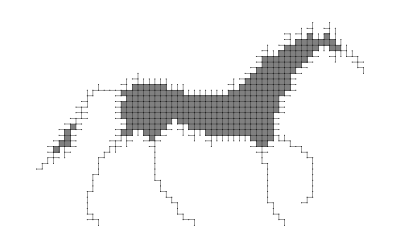

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

227

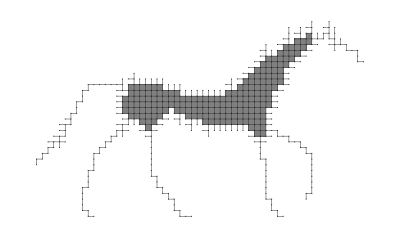

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

178

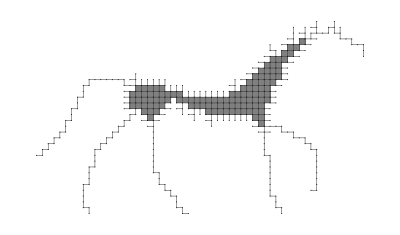

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

144

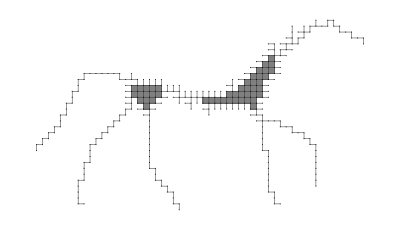

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

105

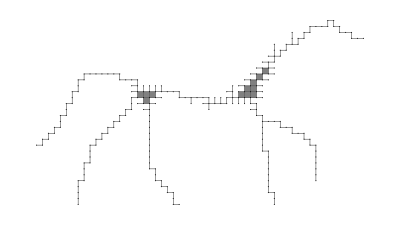

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

53

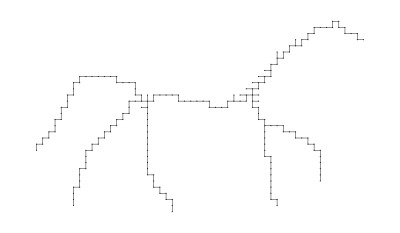

```mathematica
{numPT,pt,ct}=removeKilledParentIndex[numPT,pt,ct,kft,cc];
isoTable=setIsoTable[pt,kthIter,isoTable,cc];
kthIter++;
{kft,spNum}=updateDisjoint[numPT,kft,ct,cc];
{kft,spNum}=oneCellExclusionTest1[kft,isoTable,isE,pt,kthIter,t1a,t1r,spNum];
spNum

showCC2D[restoreAfterEThinning2[kft,cc]]
```

```mathematica
Dimensions[isoTable]⟦1⟧
```

3

```mathematica
Length[isoTable⟦1⟧]
```

1036

```mathematica
1888
isoTable
```

1888

```mathematica
Length[horse8[[2]]]
```

1888